```mathematica
Clear["Global`*"];
dd={x,y,z};
a={x-x0 ,y-y0,z-z0};
b={dx ,dy ,dz}/Sqrt[dx^2+dy^2+dz^2];
temp=Cross[a,b];
temp2=Simplify[temp.temp]
Simplify[D[temp2,{dd}]]
```

1/(dx^2+dy^2+dz^2)(dz^2 (x^2-2 x x0+x0^2+(y-y0)^2)-2 dy (y-y0) (dx (x-x0)+dz (z-z0))+dy^2 (x^2-2 x x0+x0^2+(z-z0)^2)+dx^2 (y^2-2 y y0+y0^2+(z-z0)^2)-2 dx dz (x-x0) (z-z0))

{-(2 (dy^2 (-x+x0)+dx dy (y-y0)+dz (dz (-x+x0)+dx (z-z0))))/(dx^2+dy^2+dz^2),(2 (dx dy (-x+x0)+dx^2 (y-y0)+dz (dz (y-y0)+dy (-z+z0))))/(dx^2+dy^2+dz^2),(2 (dx dz (-x+x0)+dy (dz (-y+y0)+dy (z-z0))+dx^2 (z-z0)))/(dx^2+dy^2+dz^2)}

```mathematica
temp
```

{(dz y)/(dx^2+dy^2+dz^2)-(dz y0)/(dx^2+dy^2+dz^2)-(dy z)/(dx^2+dy^2+dz^2)+(dy z0)/(dx^2+dy^2+dz^2),-(dz x)/(dx^2+dy^2+dz^2)+(dz x0)/(dx^2+dy^2+dz^2)+(dx z)/(dx^2+dy^2+dz^2)-(dx z0)/(dx^2+dy^2+dz^2),(dy x)/(dx^2+dy^2+dz^2)-(dy x0)/(dx^2+dy^2+dz^2)-(dx y)/(dx^2+dy^2+dz^2)+(dx y0)/(dx^2+dy^2+dz^2)}

```mathematica
D[Sqrt[zz],zz]
```

1/(2 √zz)

```mathematica
j=(dy^2 (2 x-2 x0)+dz^2 (2 x-2 x0)-2 dx dy (y-y0)-2 dx dz (z-z0))/2
```

1/2 (dy^2 (2 x-2 x0)+dz^2 (2 x-2 x0)-2 dx dy (y-y0)-2 dx dz (z-z0))

```mathematica
Simplify[j]
```

dy^2 (x-x0)+dx dy (-y+y0)+dz (dz (x-x0)+dx (-z+z0))

```mathematica
k=(dx^2 (2 y-2 y0)+2 dz^2 (y-y0)-2 dy (dx (x-x0)+dz (z-z0)))/2
```

1/2 (dx^2 (2 y-2 y0)+2 dz^2 (y-y0)-2 dy (dx (x-x0)+dz (z-z0)))

```mathematica
Simplify[k]
```

dx dy (-x+x0)+dx^2 (y-y0)+dz (dz (y-y0)+dy (-z+z0))

```mathematica
l=(-2 dx dz (x-x0)-2 dy dz (y-y0)+2 dx^2 (z-z0)+2 dy^2 (z-z0))/2
```

1/2 (-2 dx dz (x-x0)-2 dy dz (y-y0)+2 dx^2 (z-z0)+2 dy^2 (z-z0))

```mathematica
Simplify[l]
```

dx dz (-x+x0)+dy (dz (-y+y0)+dy (z-z0))+dx^2 (z-z0)

```mathematica
CForm[dy^2 (x-x0)+dx dy (-y+y0)+dz (dz (x-x0)+dx (-z+z0))]
```

Power(dy,2)*(x - x0) + dx*dy*(-y + y0) + dz*(dz*(x - x0) + dx*(-z + z0))

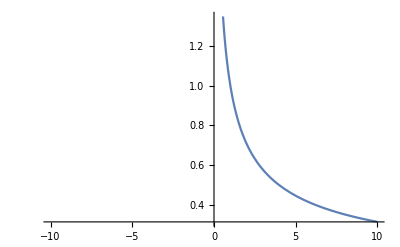

```mathematica
Plot[1/Sqrt[α],{α,-10,10}]
```